```mathematica
SetDirectory["C:\\Users\\Ксения\\palabos\\examples\\showCases\\boundaryCondition\\tmp"]
```

C:\Users\Ксения\palabos\examples\showCases\boundaryCondition\tmp

```mathematica
a= Import["dens_en.dat"]
```

{{1000,0.0999,1.,8.67856×10^-6},{2000,0.1999,1.,0.0000122528},{3000,0.2999,1.,0.0000152225},{4000,0.3999,1.,0.0000178975},{5000,0.4999,1.,0.0000202645},{6000,0.5999,1.,0.0000222952},{7000,0.6999,1.,0.0000239938},{8000,0.7999,1.,0.0000253886},{9000,0.8999,1.,0.0000265187},{10000,0.9999,1.,0.0000274254},{11000,1.0999,1.,0.0000281478},{12000,1.1999,1.,0.0000287202},{13000,1.2999,1.,0.0000291719},{14000,1.3999,1.,0.0000295274},{15000,1.4999,1.,0.0000298064},{16000,1.5999,1.,0.000030025},{17000,1.6999,1.,0.0000301961},{18000,1.7999,1.,0.0000303299},{19000,1.8999,1.,0.0000304343},{20000,1.9999,1.,0.0000305159},{21000,2.0999,1.,0.0000305795},{22000,2.1999,1.,0.0000306291},{23000,2.2999,1.,0.0000306678},{24000,2.3999,1.,0.0000306979},{25000,2.4999,1.,0.0000307214},{26000,2.5999,1.,0.0000307397},{27000,2.6999,1.,0.000030754},{28000,2.7999,1.,0.0000307651},{29000,2.8999,1.,0.0000307737},{30000,2.9999,1.,0.0000307805},{31000,3.0999,1.,0.0000307857},{32000,3.1999,1.,0.0000307898},{33000,3.2999,1.,0.000030793},{34000,3.3999,1.,0.0000307955},{35000,3.4999,1.,0.0000307974},{36000,3.5999,1.,0.0000307989},{37000,3.6999,1.,0.0000308001},{38000,3.7999,1.,0.000030801},{39000,3.8999,1.,0.0000308017},{40000,3.9999,1.,0.0000308023},{41000,4.0999,1.,0.0000308027},{42000,4.1999,1.,0.0000308031},{43000,4.2999,1.,0.0000308033},{44000,4.3999,1.,0.0000308035},{45000,4.4999,1.,0.0000308037},{46000,4.5999,1.,0.0000308038},{47000,4.6999,1.,0.0000308039},{48000,4.7999,1.,0.000030804},{49000,4.8999,1.,0.000030804},{50000,4.9999,1.,0.0000308041},{51000,5.0999,1.,0.0000308041},{52000,5.1999,1.,0.0000308041},{53000,5.2999,1.,0.0000308042},{54000,5.3999,1.,0.0000308042},{55000,5.4999,1.,0.0000308042},{56000,5.5999,1.,0.0000308042},{57000,5.6999,1.,0.0000308042},{58000,5.7999,1.,0.0000308042},{59000,5.8999,1.,0.0000308042},{60000,5.9999,1.,0.0000308042},{61000,6.0999,1.,0.0000308042},{62000,6.1999,1.,0.0000308042},{63000,6.2999,1.,0.0000308042},{64000,6.3999,1.,0.0000308042},{65000,6.4999,1.,0.0000308042},{66000,6.5999,1.,0.0000308042},{67000,6.6999,1.,0.0000308042},{68000,6.7999,1.,0.0000308042},{69000,6.8999,1.,0.0000308042},{70000,6.9999,1.,0.0000308042},{71000,7.0999,1.,0.0000308042},{72000,7.1999,1.,0.0000308042},{73000,7.2999,1.,0.0000308042},{74000,7.3999,1.,0.0000308042},{75000,7.4999,1.,0.0000308042},{76000,7.5999,1.,0.0000308042},{77000,7.6999,1.,0.0000308042},{78000,7.7999,1.,0.0000308042},{79000,7.8999,1.,0.0000308042},{80000,7.9999,1.,0.0000308042},{81000,8.0999,1.,0.0000308042},{82000,8.1999,1.,0.0000308042},{83000,8.2999,1.,0.0000308042},{84000,8.3999,1.,0.0000308042},{85000,8.4999,1.,0.0000308042},{86000,8.5999,1.,0.0000308042},{87000,8.6999,1.,0.0000308042},{88000,8.7999,1.,0.0000308042},{89000,8.8999,1.,0.0000308042},{90000,8.9999,1.,0.0000308042},{91000,9.0999,1.,0.0000308042},{92000,9.1999,1.,0.0000308042},{93000,9.2999,1.,0.0000308042},{94000,9.3999,1.,0.0000308042},{95000,9.4999,1.,0.0000308042},{96000,9.5999,1.,0.0000308042},{97000,9.6999,1.,0.0000308042},{98000,9.7999,1.,0.0000308042},{99000,9.8999,1.,0.0000308042},{100000,9.9999,1.,0.0000308042},{101000,10.0999,1.,0.0000308042},{102000,10.1999,1.,0.0000308042},{103000,10.2999,1.,0.0000308042},{104000,10.3999,1.,0.0000308042},{105000,10.4999,1.,0.0000308042},{106000,10.5999,1.,0.0000308042},{107000,10.6999,1.,0.0000308042},{108000,10.7999,1.,0.0000308042},{109000,10.8999,1.,0.0000308042},{110000,10.9999,1.,0.0000308042},{111000,11.0999,1.,0.0000308042},{112000,11.1999,1.,0.0000308042},{113000,11.2999,1.,0.0000308042},{114000,11.3999,1.,0.0000308042},{115000,11.4999,1.,0.0000308042},{116000,11.5999,1.,0.0000308042},{117000,11.6999,1.,0.0000308042},{118000,11.7999,1.,0.0000308042},{119000,11.8999,1.,0.0000308042},{120000,11.9999,1.,0.0000308042},{121000,12.0999,1.,0.0000308042},{122000,12.1999,1.,0.0000308042},{123000,12.2999,1.,0.0000308042},{124000,12.3999,1.,0.0000308042},{125000,12.4999,1.,0.0000308042},{126000,12.5999,1.,0.0000308042},{127000,12.6999,1.,0.0000308042},{128000,12.7999,1.,0.0000308042},{129000,12.8999,1.,0.0000308042},{130000,12.9999,1.,0.0000308042},{131000,13.0999,1.,0.0000308042},{132000,13.1999,1.,0.0000308042},{133000,13.2999,1.,0.0000308042},{134000,13.3999,1.,0.0000308042},{135000,13.4999,1.,0.0000308042},{136000,13.5999,1.,0.0000308042},{137000,13.6999,1.,0.0000308042},{138000,13.7999,1.,0.0000308042},{139000,13.8999,1.,0.0000308042},{140000,13.9999,1.,0.0000308042},{141000,14.0999,1.,0.0000308042},{142000,14.1999,1.,0.0000308042},{143000,14.2999,1.,0.0000308042},{144000,14.3999,1.,0.0000308042},{145000,14.4999,1.,0.0000308042},{146000,14.5999,1.,0.0000308042},{147000,14.6999,1.,0.0000308042},{148000,14.7999,1.,0.0000308042},{149000,14.8999,1.,0.0000308042},{150000,14.9999,1.,0.0000308042},{151000,15.0999,1.,0.0000308042},{152000,15.1999,1.,0.0000308042},{153000,15.2999,1.,0.0000308042},{154000,15.3999,1.,0.0000308042},{155000,15.4999,1.,0.0000308042},{156000,15.5999,1.,0.0000308042},{157000,15.6999,1.,0.0000308042},{158000,15.7999,1.,0.0000308042},{159000,15.8999,1.,0.0000308042},{160000,15.9999,1.,0.0000308042},{161000,16.0999,1.,0.0000308042},{162000,16.1999,1.,0.0000308042},{163000,16.2999,1.,0.0000308042},{164000,16.3999,1.,0.0000308042},{165000,16.4999,1.,0.0000308042},{166000,16.5999,1.,0.0000308042},{167000,16.6999,1.,0.0000308042},{168000,16.7999,1.,0.0000308042},{169000,16.8999,1.,0.0000308042},{170000,16.9999,1.,0.0000308042},{171000,17.0999,1.,0.0000308042},{172000,17.1999,1.,0.0000308042},{173000,17.2999,1.,0.0000308042},{174000,17.3999,1.,0.0000308042},{175000,17.4999,1.,0.0000308042},{176000,17.5999,1.,0.0000308042},{177000,17.6999,1.,0.0000308042},{178000,17.7999,1.,0.0000308042},{179000,17.8999,1.,0.0000308042},{180000,17.9999,1.,0.0000308042},{181000,18.0999,1.,0.0000308042},{182000,18.1999,1.,0.0000308042},{183000,18.2999,1.,0.0000308042},{184000,18.3999,1.,0.0000308042},{185000,18.4999,1.,0.0000308042},{186000,18.5999,1.,0.0000308042},{187000,18.6999,1.,0.0000308042},{188000,18.7999,1.,0.0000308042},{189000,18.8999,1.,0.0000308042},{190000,18.9999,1.,0.0000308042},{191000,19.0999,1.,0.0000308042},{192000,19.1999,1.,0.0000308042},{193000,19.2999,1.,0.0000308042},{194000,19.3999,1.,0.0000308042},{195000,19.4999,1.,0.0000308042},{196000,19.5999,1.,0.0000308042},{197000,19.6999,1.,0.0000308042},{198000,19.7999,1.,0.0000308042},{199000,19.8999,1.,0.0000308042},{200000,19.9999,1.,0.0000308042},{201000,20.0999,1.,0.0000308042},{202000,20.1999,1.,0.0000308042},{203000,20.2999,1.,0.0000308042},{204000,20.3999,1.,0.0000308042},{205000,20.4999,1.,0.0000308042},{206000,20.5999,1.,0.0000308042},{207000,20.6999,1.,0.0000308042},{208000,20.7999,1.,0.0000308042},{209000,20.8999,1.,0.0000308042},{210000,20.9999,1.,0.0000308042},{211000,21.0999,1.,0.0000308042},{212000,21.1999,1.,0.0000308042},{213000,21.2999,1.,0.0000308042},{214000,21.3999,1.,0.0000308042},{215000,21.4999,1.,0.0000308042},{216000,21.5999,1.,0.0000308042},{217000,21.6999,1.,0.0000308042},{218000,21.7999,1.,0.0000308042},{219000,21.8999,1.,0.0000308042},{220000,21.9999,1.,0.0000308042},{221000,22.0999,1.,0.0000308042},{222000,22.1999,1.,0.0000308042},{223000,22.2999,1.,0.0000308042},{224000,22.3999,1.,0.0000308042},{225000,22.4999,1.,0.0000308042},{226000,22.5999,1.,0.0000308042},{227000,22.6999,1.,0.0000308042},{228000,22.7999,1.,0.0000308042},{229000,22.8999,1.,0.0000308042},{230000,22.9999,1.,0.0000308042},{231000,23.0999,1.,0.0000308042},{232000,23.1999,1.,0.0000308042},{233000,23.2999,1.,0.0000308042},{234000,23.3999,1.,0.0000308042},{235000,23.4999,1.,0.0000308042},{236000,23.5999,1.,0.0000308042},{237000,23.6999,1.,0.0000308042},{238000,23.7999,1.,0.0000308042},{239000,23.8999,1.,0.0000308042},{240000,23.9999,1.,0.0000308042},{241000,24.0999,1.,0.0000308042},{242000,24.1999,1.,0.0000308042},{243000,24.2999,1.,0.0000308042},{244000,24.3999,1.,0.0000308042},{245000,24.4999,1.,0.0000308042},{246000,24.5999,1.,0.0000308042},{247000,24.6999,1.,0.0000308042},{248000,24.7999,1.,0.0000308042},{249000,24.8999,1.,0.0000308042},{250000,24.9999,1.,0.0000308042},{251000,25.0999,1.,0.0000308042},{252000,25.1999,1.,0.0000308042},{253000,25.2999,1.,0.0000308042},{254000,25.3999,1.,0.0000308042},{255000,25.4999,1.,0.0000308042},{256000,25.5999,1.,0.0000308042},{257000,25.6999,1.,0.0000308042},{258000,25.7999,1.,0.0000308042},{259000,25.8999,1.,0.0000308042},{260000,25.9999,1.,0.0000308042},{261000,26.0999,1.,0.0000308042},{262000,26.1999,1.,0.0000308042},{263000,26.2999,1.,0.0000308042},{264000,26.3999,1.,0.0000308042},{265000,26.4999,1.,0.0000308042},{266000,26.5999,1.,0.0000308042},{267000,26.6999,1.,0.0000308042},{268000,26.7999,1.,0.0000308042},{269000,26.8999,1.00001,0.0000308042},{270000,26.9999,1.00001,0.0000308042},{271000,27.0999,1.00001,0.0000308042},{272000,27.1999,1.00001,0.0000308042},{273000,27.2999,1.00001,0.0000308042},{274000,27.3999,1.00001,0.0000308042},{275000,27.4999,1.00001,0.0000308042},{276000,27.5999,1.00001,0.0000308042},{277000,27.6999,1.00001,0.0000308042},{278000,27.7999,1.00001,0.0000308042},{279000,27.8999,1.00001,0.0000308042},{280000,27.9999,1.00001,0.0000308042},{281000,28.0999,1.00001,0.0000308042},{282000,28.1999,1.00001,0.0000308042},{283000,28.2999,1.00001,0.0000308042},{284000,28.3999,1.00001,0.0000308042},{285000,28.4999,1.00001,0.0000308042},{286000,28.5999,1.00001,0.0000308042},{287000,28.6999,1.00001,0.0000308042},{288000,28.7999,1.00001,0.0000308042},{289000,28.8999,1.00001,0.0000308042},{290000,28.9999,1.00001,0.0000308042},{291000,29.0999,1.00001,0.0000308042},{292000,29.1999,1.00001,0.0000308042},{293000,29.2999,1.00001,0.0000308042},{294000,29.3999,1.00001,0.0000308042},{295000,29.4999,1.00001,0.0000308042},{296000,29.5999,1.00001,0.0000308042},{297000,29.6999,1.00001,0.0000308042},{298000,29.7999,1.00001,0.0000308042},{299000,29.8999,1.00001,0.0000308042},{300000,29.9999,1.00001,0.0000308042},{301000,30.0999,1.00001,0.0000308042},{302000,30.1999,1.00001,0.0000308042},{303000,30.2999,1.00001,0.0000308042},{304000,30.3999,1.00001,0.0000308042},{305000,30.4999,1.00001,0.0000308042},{306000,30.5999,1.00001,0.0000308042},{307000,30.6999,1.00001,0.0000308042},{308000,30.7999,1.00001,0.0000308042},{309000,30.8999,1.00001,0.0000308042},{310000,30.9999,1.00001,0.0000308042},{311000,31.0999,1.00001,0.0000308042},{312000,31.1999,1.00001,0.0000308042},{313000,31.2999,1.00001,0.0000308042},{314000,31.3999,1.00001,0.0000308042},{315000,31.4999,1.00001,0.0000308042},{316000,31.5999,1.00001,0.0000308042},{317000,31.6999,1.00001,0.0000308042},{318000,31.7999,1.00001,0.0000308042},{319000,31.8999,1.00001,0.0000308042},{320000,31.9999,1.00001,0.0000308042},{321000,32.0999,1.00001,0.0000308042},{322000,32.1999,1.00001,0.0000308042},{323000,32.2999,1.00001,0.0000308042},{324000,32.3999,1.00001,0.0000308042},{325000,32.4999,1.00001,0.0000308042},{326000,32.5999,1.00001,0.0000308042},{327000,32.6999,1.00001,0.0000308042},{328000,32.7999,1.00001,0.0000308042},{329000,32.8999,1.00001,0.0000308042},{330000,32.9999,1.00001,0.0000308042},{331000,33.0999,1.00001,0.0000308042},{332000,33.1999,1.00001,0.0000308042},{333000,33.2999,1.00001,0.0000308042},{334000,33.3999,1.00001,0.0000308042},{335000,33.4999,1.00001,0.0000308042},{336000,33.5999,1.00001,0.0000308042},{337000,33.6999,1.00001,0.0000308042},{338000,33.7999,1.00001,0.0000308042},{339000,33.8999,1.00001,0.0000308042},{340000,33.9999,1.00001,0.0000308042},{341000,34.0999,1.00001,0.0000308042},{342000,34.1999,1.00001,0.0000308042},{343000,34.2999,1.00001,0.0000308042},{344000,34.3999,1.00001,0.0000308042},{345000,34.4999,1.00001,0.0000308042},{346000,34.5999,1.00001,0.0000308042},{347000,34.6999,1.00001,0.0000308042},{348000,34.7999,1.00001,0.0000308042},{349000,34.8999,1.00001,0.0000308042},{350000,34.9999,1.00001,0.0000308042},{351000,35.0999,1.00001,0.0000308042},{352000,35.1999,1.00001,0.0000308042},{353000,35.2999,1.00001,0.0000308042},{354000,35.3999,1.00001,0.0000308042},{355000,35.4999,1.00001,0.0000308042},{356000,35.5999,1.00001,0.0000308042},{357000,35.6999,1.00001,0.0000308042},{358000,35.7999,1.00001,0.0000308042},{359000,35.8999,1.00001,0.0000308042},{360000,35.9999,1.00001,0.0000308042},{361000,36.0999,1.00001,0.0000308042},{362000,36.1999,1.00001,0.0000308042},{363000,36.2999,1.00001,0.0000308042},{364000,36.3999,1.00001,0.0000308042},{365000,36.4999,1.00001,0.0000308042},{366000,36.5999,1.00001,0.0000308042},{367000,36.6999,1.00001,0.0000308042},{368000,36.7999,1.00001,0.0000308042},{369000,36.8999,1.00001,0.0000308042},{370000,36.9999,1.00001,0.0000308042},{371000,37.0999,1.00001,0.0000308042},{372000,37.1999,1.00001,0.0000308042},{373000,37.2999,1.00001,0.0000308042},{374000,37.3999,1.00001,0.0000308042},{375000,37.4999,1.00001,0.0000308042},{376000,37.5999,1.00001,0.0000308042},{377000,37.6999,1.00001,0.0000308042},{378000,37.7999,1.00001,0.0000308042},{379000,37.8999,1.00001,0.0000308042},{380000,37.9999,1.00001,0.0000308042},{381000,38.0999,1.00001,0.0000308042},{382000,38.1999,1.00001,0.0000308042},{383000,38.2999,1.00001,0.0000308042},{384000,38.3999,1.00001,0.0000308042},{385000,38.4999,1.00001,0.0000308042},{386000,38.5999,1.00001,0.0000308042},{387000,38.6999,1.00001,0.0000308042},{388000,38.7999,1.00001,0.0000308042},{389000,38.8999,1.00001,0.0000308042},{390000,38.9999,1.00001,0.0000308042},{391000,39.0999,1.00001,0.0000308042},{392000,39.1999,1.00001,0.0000308042},{393000,39.2999,1.00001,0.0000308042},{394000,39.3999,1.00001,0.0000308042},{395000,39.4999,1.00001,0.0000308042},{396000,39.5999,1.00001,0.0000308042},{397000,39.6999,1.00001,0.0000308042},{398000,39.7999,1.00001,0.0000308042},{399000,39.8999,1.00001,0.0000308042},{400000,39.9999,1.00001,0.0000308042},{401000,40.0999,1.00001,0.0000308042},{402000,40.1999,1.00001,0.0000308042},{403000,40.2999,1.00001,0.0000308042},{404000,40.3999,1.00001,0.0000308042},{405000,40.4999,1.00001,0.0000308042},{406000,40.5999,1.00001,0.0000308042},{407000,40.6999,1.00001,0.0000308042},{408000,40.7999,1.00001,0.0000308042},{409000,40.8999,1.00001,0.0000308042},{410000,40.9999,1.00001,0.0000308042},{411000,41.0999,1.00001,0.0000308042},{412000,41.1999,1.00001,0.0000308042},{413000,41.2999,1.00001,0.0000308042},{414000,41.3999,1.00001,0.0000308042},{415000,41.4999,1.00001,0.0000308042},{416000,41.5999,1.00001,0.0000308042},{417000,41.6999,1.00001,0.0000308042},{418000,41.7999,1.00001,0.0000308042},{419000,41.8999,1.00001,0.0000308042},{420000,41.9999,1.00001,0.0000308042},{421000,42.0999,1.00001,0.0000308042},{422000,42.1999,1.00001,0.0000308042},{423000,42.2999,1.00001,0.0000308042},{424000,42.3999,1.00001,0.0000308042},{425000,42.4999,1.00001,0.0000308042},{426000,42.5999,1.00001,0.0000308042},{427000,42.6999,1.00001,0.0000308042},{428000,42.7999,1.00001,0.0000308042},{429000,42.8999,1.00001,0.0000308042},{430000,42.9999,1.00001,0.0000308042},{431000,43.0999,1.00001,0.0000308042},{432000,43.1999,1.00001,0.0000308042},{433000,43.2999,1.00001,0.0000308042},{434000,43.3999,1.00001,0.0000308042},{435000,43.4999,1.00001,0.0000308042},{436000,43.5999,1.00001,0.0000308042},{437000,43.6999,1.00001,0.0000308042},{438000,43.7999,1.00001,0.0000308042},{439000,43.8999,1.00001,0.0000308042},{440000,43.9999,1.00001,0.0000308042},{441000,44.0999,1.00001,0.0000308042},{442000,44.1999,1.00001,0.0000308042},{443000,44.2999,1.00001,0.0000308042},{444000,44.3999,1.00001,0.0000308042},{445000,44.4999,1.00001,0.0000308042},{446000,44.5999,1.00001,0.0000308042},{447000,44.6999,1.00001,0.0000308042},{448000,44.7999,1.00001,0.0000308042},{449000,44.8999,1.00001,0.0000308042},{450000,44.9999,1.00001,0.0000308042},{451000,45.0999,1.00001,0.0000308042},{452000,45.1999,1.00001,0.0000308042},{453000,45.2999,1.00001,0.0000308042},{454000,45.3999,1.00001,0.0000308042},{455000,45.4999,1.00001,0.0000308042},{456000,45.5999,1.00001,0.0000308042},{457000,45.6999,1.00001,0.0000308042},{458000,45.7999,1.00001,0.0000308042},{459000,45.8999,1.00001,0.0000308042},{460000,45.9999,1.00001,0.0000308042},{461000,46.0999,1.00001,0.0000308042},{462000,46.1999,1.00001,0.0000308042},{463000,46.2999,1.00001,0.0000308042},{464000,46.3999,1.00001,0.0000308042},{465000,46.4999,1.00001,0.0000308042},{466000,46.5999,1.00001,0.0000308042},{467000,46.6999,1.00001,0.0000308042},{468000,46.7999,1.00001,0.0000308042},{469000,46.8999,1.00001,0.0000308042},{470000,46.9999,1.00001,0.0000308042},{471000,47.0999,1.00001,0.0000308042},{472000,47.1999,1.00001,0.0000308042},{473000,47.2999,1.00001,0.0000308042},{474000,47.3999,1.00001,0.0000308042},{475000,47.4999,1.00001,0.0000308042},{476000,47.5999,1.00001,0.0000308042},{477000,47.6999,1.00001,0.0000308042},{478000,47.7999,1.00001,0.0000308042},{479000,47.8999,1.00001,0.0000308042},{480000,47.9999,1.00001,0.0000308042},{481000,48.0999,1.00001,0.0000308042},{482000,48.1999,1.00001,0.0000308042},{483000,48.2999,1.00001,0.0000308042},{484000,48.3999,1.00001,0.0000308042},{485000,48.4999,1.00001,0.0000308042},{486000,48.5999,1.00001,0.0000308042},{487000,48.6999,1.00001,0.0000308042},{488000,48.7999,1.00001,0.0000308042},{489000,48.8999,1.00001,0.0000308042},{490000,48.9999,1.00001,0.0000308042},{491000,49.0999,1.00001,0.0000308042},{492000,49.1999,1.00001,0.0000308042},{493000,49.2999,1.00001,0.0000308042},{494000,49.3999,1.00001,0.0000308042},{495000,49.4999,1.00001,0.0000308042},{496000,49.5999,1.00001,0.0000308042},{497000,49.6999,1.00001,0.0000308042},{498000,49.7999,1.00001,0.0000308042},{499000,49.8999,1.00001,0.0000308042},{500000,49.9999,1.00001,0.0000308042},{501000,50.0999,1.00001,0.0000308042},{502000,50.1999,1.00001,0.0000308042},{503000,50.2999,1.00001,0.0000308042},{504000,50.3999,1.00001,0.0000308042},{505000,50.4999,1.00001,0.0000308042},{506000,50.5999,1.00001,0.0000308042},{507000,50.6999,1.00001,0.0000308042},{508000,50.7999,1.00001,0.0000308042},{509000,50.8999,1.00001,0.0000308042},{510000,50.9999,1.00001,0.0000308042},{511000,51.0999,1.00001,0.0000308042},{512000,51.1999,1.00001,0.0000308042},{513000,51.2999,1.00001,0.0000308042},{514000,51.3999,1.00001,0.0000308042},{515000,51.4999,1.00001,0.0000308042},{516000,51.5999,1.00001,0.0000308042},{517000,51.6999,1.00001,0.0000308042},{518000,51.7999,1.00001,0.0000308042},{519000,51.8999,1.00001,0.0000308042},{520000,51.9999,1.00001,0.0000308042},{521000,52.0999,1.00001,0.0000308042},{522000,52.1999,1.00001,0.0000308042},{523000,52.2999,1.00001,0.0000308042},{524000,52.3999,1.00001,0.0000308042},{525000,52.4999,1.00001,0.0000308042},{526000,52.5999,1.00001,0.0000308042},{527000,52.6999,1.00001,0.0000308042},{528000,52.7999,1.00001,0.0000308042},{529000,52.8999,1.00001,0.0000308042},{530000,52.9999,1.00001,0.0000308042},{531000,53.0999,1.00001,0.0000308042},{532000,53.1999,1.00001,0.0000308042},{533000,53.2999,1.00001,0.0000308042},{534000,53.3999,1.00001,0.0000308042},{535000,53.4999,1.00001,0.0000308042},{536000,53.5999,1.00001,0.0000308042},{537000,53.6999,1.00001,0.0000308042},{538000,53.7999,1.00001,0.0000308042},{539000,53.8999,1.00001,0.0000308042},{540000,53.9999,1.00001,0.0000308042},{541000,54.0999,1.00001,0.0000308042},{542000,54.1999,1.00001,0.0000308042},{543000,54.2999,1.00001,0.0000308042},{544000,54.3999,1.00001,0.0000308042},{545000,54.4999,1.00001,0.0000308042},{546000,54.5999,1.00001,0.0000308042},{547000,54.6999,1.00001,0.0000308042},{548000,54.7999,1.00001,0.0000308042},{549000,54.8999,1.00001,0.0000308042},{550000,54.9999,1.00001,0.0000308042},{551000,55.0999,1.00001,0.0000308042},{552000,55.1999,1.00001,0.0000308042},{553000,55.2999,1.00001,0.0000308042},{554000,55.3999,1.00001,0.0000308042},{555000,55.4999,1.00001,0.0000308042},{556000,55.5999,1.00001,0.0000308042},{557000,55.6999,1.00001,0.0000308042},{558000,55.7999,1.00001,0.0000308042},{559000,55.8999,1.00001,0.0000308042},{560000,55.9999,1.00001,0.0000308042},{561000,56.0999,1.00001,0.0000308042},{562000,56.1999,1.00001,0.0000308042},{563000,56.2999,1.00001,0.0000308042},{564000,56.3999,1.00001,0.0000308042},{565000,56.4999,1.00001,0.0000308042},{566000,56.5999,1.00001,0.0000308042},{567000,56.6999,1.00001,0.0000308042},{568000,56.7999,1.00001,0.0000308042},{569000,56.8999,1.00001,0.0000308042},{570000,56.9999,1.00001,0.0000308042},{571000,57.0999,1.00001,0.0000308042},{572000,57.1999,1.00001,0.0000308042},{573000,57.2999,1.00001,0.0000308042},{574000,57.3999,1.00001,0.0000308042},{575000,57.4999,1.00001,0.0000308042},{576000,57.5999,1.00001,0.0000308042},{577000,57.6999,1.00001,0.0000308042},{578000,57.7999,1.00001,0.0000308042},{579000,57.8999,1.00001,0.0000308042},{580000,57.9999,1.00001,0.0000308042},{581000,58.0999,1.00001,0.0000308042},{582000,58.1999,1.00001,0.0000308042},{583000,58.2999,1.00001,0.0000308042},{584000,58.3999,1.00001,0.0000308042},{585000,58.4999,1.00001,0.0000308042},{586000,58.5999,1.00001,0.0000308042},{587000,58.6999,1.00001,0.0000308042},{588000,58.7999,1.00001,0.0000308042},{589000,58.8999,1.00001,0.0000308042},{590000,58.9999,1.00001,0.0000308042},{591000,59.0999,1.00001,0.0000308042},{592000,59.1999,1.00001,0.0000308042},{593000,59.2999,1.00001,0.0000308042},{594000,59.3999,1.00001,0.0000308042},{595000,59.4999,1.00001,0.0000308042},{596000,59.5999,1.00001,0.0000308042},{597000,59.6999,1.00001,0.0000308042},{598000,59.7999,1.00001,0.0000308042},{599000,59.8999,1.00001,0.0000308042},{600000,59.9999,1.00001,0.0000308042},{601000,60.0999,1.00001,0.0000308042},{602000,60.1999,1.00001,0.0000308042},{603000,60.2999,1.00001,0.0000308042},{604000,60.3999,1.00001,0.0000308042},{605000,60.4999,1.00001,0.0000308042},{606000,60.5999,1.00001,0.0000308042},{607000,60.6999,1.00001,0.0000308042},{608000,60.7999,1.00001,0.0000308042},{609000,60.8999,1.00001,0.0000308042},{610000,60.9999,1.00001,0.0000308042},{611000,61.0999,1.00001,0.0000308042},{612000,61.1999,1.00001,0.0000308042},{613000,61.2999,1.00001,0.0000308042},{614000,61.3999,1.00001,0.0000308042},{615000,61.4999,1.00001,0.0000308042},{616000,61.5999,1.00001,0.0000308042},{617000,61.6999,1.00001,0.0000308042},{618000,61.7999,1.00001,0.0000308042},{619000,61.8999,1.00001,0.0000308042},{620000,61.9999,1.00001,0.0000308042},{621000,62.0999,1.00001,0.0000308042},{622000,62.1999,1.00001,0.0000308042},{623000,62.2999,1.00001,0.0000308042},{624000,62.3999,1.00001,0.0000308042},{625000,62.4999,1.00001,0.0000308042},{626000,62.5999,1.00001,0.0000308042},{627000,62.6999,1.00001,0.0000308042},{628000,62.7999,1.00001,0.0000308042},{629000,62.8999,1.00001,0.0000308042},{630000,62.9999,1.00001,0.0000308042},{631000,63.0999,1.00001,0.0000308042},{632000,63.1999,1.00001,0.0000308042},{633000,63.2999,1.00001,0.0000308042},{634000,63.3999,1.00001,0.0000308042},{635000,63.4999,1.00001,0.0000308042},{636000,63.5999,1.00001,0.0000308042},{637000,63.6999,1.00001,0.0000308042},{638000,63.7999,1.00001,0.0000308042},{639000,63.8999,1.00001,0.0000308042},{640000,63.9999,1.00001,0.0000308042},{641000,64.0999,1.00001,0.0000308042},{642000,64.1999,1.00001,0.0000308042},{643000,64.2999,1.00001,0.0000308042},{644000,64.3999,1.00001,0.0000308042},{645000,64.4999,1.00001,0.0000308042},{646000,64.5999,1.00001,0.0000308042},{647000,64.6999,1.00001,0.0000308042},{648000,64.7999,1.00001,0.0000308042},{649000,64.8999,1.00001,0.0000308042},{650000,64.9999,1.00001,0.0000308042},{651000,65.0999,1.00001,0.0000308042},{652000,65.1999,1.00001,0.0000308042},{653000,65.2999,1.00001,0.0000308042},{654000,65.3999,1.00001,0.0000308042},{655000,65.4999,1.00001,0.0000308042},{656000,65.5999,1.00001,0.0000308042},{657000,65.6999,1.00001,0.0000308042},{658000,65.7999,1.00001,0.0000308042},{659000,65.8999,1.00001,0.0000308042},{660000,65.9999,1.00001,0.0000308042},{661000,66.0999,1.00001,0.0000308042},{662000,66.1999,1.00001,0.0000308042},{663000,66.2999,1.00001,0.0000308042},{664000,66.3999,1.00001,0.0000308042},{665000,66.4999,1.00001,0.0000308042},{666000,66.5999,1.00001,0.0000308042},{667000,66.6999,1.00001,0.0000308042},{668000,66.7999,1.00001,0.0000308042},{669000,66.8999,1.00001,0.0000308042},{670000,66.9999,1.00001,0.0000308042},{671000,67.0999,1.00001,0.0000308042},{672000,67.1999,1.00001,0.0000308042},{673000,67.2999,1.00001,0.0000308042},{674000,67.3999,1.00001,0.0000308042},{675000,67.4999,1.00001,0.0000308042},{676000,67.5999,1.00001,0.0000308042},{677000,67.6999,1.00001,0.0000308042},{678000,67.7999,1.00001,0.0000308042},{679000,67.8999,1.00001,0.0000308042},{680000,67.9999,1.00001,0.0000308042},{681000,68.0999,1.00001,0.0000308042},{682000,68.1999,1.00001,0.0000308042},{683000,68.2999,1.00001,0.0000308042},{684000,68.3999,1.00001,0.0000308042},{685000,68.4999,1.00001,0.0000308042},{686000,68.5999,1.00001,0.0000308042},{687000,68.6999,1.00001,0.0000308042},{688000,68.7999,1.00001,0.0000308042},{689000,68.8999,1.00001,0.0000308042},{690000,68.9999,1.00001,0.0000308042},{691000,69.0999,1.00001,0.0000308042},{692000,69.1999,1.00001,0.0000308042},{693000,69.2999,1.00001,0.0000308042},{694000,69.3999,1.00001,0.0000308042},{695000,69.4999,1.00001,0.0000308042},{696000,69.5999,1.00001,0.0000308042},{697000,69.6999,1.00001,0.0000308042},{698000,69.7999,1.00001,0.0000308042},{699000,69.8999,1.00001,0.0000308042},{700000,69.9999,1.00001,0.0000308042},{701000,70.0999,1.00001,0.0000308042},{702000,70.1999,1.00001,0.0000308042},{703000,70.2999,1.00001,0.0000308042},{704000,70.3999,1.00001,0.0000308042},{705000,70.4999,1.00001,0.0000308042},{706000,70.5999,1.00001,0.0000308042},{707000,70.6999,1.00001,0.0000308042},{708000,70.7999,1.00001,0.0000308042},{709000,70.8999,1.00001,0.0000308042},{710000,70.9999,1.00001,0.0000308042},{711000,71.0999,1.00001,0.0000308042},{712000,71.1999,1.00001,0.0000308042},{713000,71.2999,1.00001,0.0000308042},{714000,71.3999,1.00001,0.0000308042},{715000,71.4999,1.00001,0.0000308042},{716000,71.5999,1.00001,0.0000308042},{717000,71.6999,1.00001,0.0000308042},{718000,71.7999,1.00001,0.0000308042},{719000,71.8999,1.00001,0.0000308042},{720000,71.9999,1.00001,0.0000308042},{721000,72.0999,1.00001,0.0000308042},{722000,72.1999,1.00001,0.0000308042},{723000,72.2999,1.00001,0.0000308042},{724000,72.3999,1.00001,0.0000308042},{725000,72.4999,1.00001,0.0000308042},{726000,72.5999,1.00001,0.0000308042},{727000,72.6999,1.00001,0.0000308042},{728000,72.7999,1.00001,0.0000308042},{729000,72.8999,1.00001,0.0000308042},{730000,72.9999,1.00001,0.0000308042},{731000,73.0999,1.00001,0.0000308042},{732000,73.1999,1.00001,0.0000308042},{733000,73.2999,1.00001,0.0000308042},{734000,73.3999,1.00001,0.0000308042},{735000,73.4999,1.00001,0.0000308042},{736000,73.5999,1.00001,0.0000308042},{737000,73.6999,1.00001,0.0000308042},{738000,73.7999,1.00001,0.0000308042},{739000,73.8999,1.00001,0.0000308042},{740000,73.9999,1.00001,0.0000308042},{741000,74.0999,1.00001,0.0000308042},{742000,74.1999,1.00001,0.0000308042},{743000,74.2999,1.00001,0.0000308042},{744000,74.3999,1.00001,0.0000308042},{745000,74.4999,1.00001,0.0000308042},{746000,74.5999,1.00001,0.0000308042},{747000,74.6999,1.00001,0.0000308042},{748000,74.7999,1.00001,0.0000308042},{749000,74.8999,1.00001,0.0000308042},{750000,74.9999,1.00001,0.0000308042},{751000,75.0999,1.00001,0.0000308042},{752000,75.1999,1.00001,0.0000308042},{753000,75.2999,1.00001,0.0000308042},{754000,75.3999,1.00001,0.0000308042},{755000,75.4999,1.00001,0.0000308042},{756000,75.5999,1.00001,0.0000308042},{757000,75.6999,1.00001,0.0000308042},{758000,75.7999,1.00001,0.0000308042},{759000,75.8999,1.00001,0.0000308042},{760000,75.9999,1.00001,0.0000308042},{761000,76.0999,1.00001,0.0000308042},{762000,76.1999,1.00001,0.0000308042},{763000,76.2999,1.00001,0.0000308042},{764000,76.3999,1.00001,0.0000308042},{765000,76.4999,1.00001,0.0000308042},{766000,76.5999,1.00001,0.0000308042},{767000,76.6999,1.00001,0.0000308042},{768000,76.7999,1.00001,0.0000308042},{769000,76.8999,1.00001,0.0000308042},{770000,76.9999,1.00001,0.0000308042},{771000,77.0999,1.00001,0.0000308042},{772000,77.1999,1.00001,0.0000308042},{773000,77.2999,1.00001,0.0000308042},{774000,77.3999,1.00001,0.0000308042},{775000,77.4999,1.00001,0.0000308042},{776000,77.5999,1.00001,0.0000308042},{777000,77.6999,1.00001,0.0000308042},{778000,77.7999,1.00001,0.0000308042},{779000,77.8999,1.00001,0.0000308042},{780000,77.9999,1.00001,0.0000308042},{781000,78.0999,1.00001,0.0000308042},{782000,78.1999,1.00001,0.0000308042},{783000,78.2999,1.00001,0.0000308042},{784000,78.3999,1.00001,0.0000308042},{785000,78.4999,1.00001,0.0000308042},{786000,78.5999,1.00001,0.0000308042},{787000,78.6999,1.00001,0.0000308042},{788000,78.7999,1.00001,0.0000308042},{789000,78.8999,1.00001,0.0000308042},{790000,78.9999,1.00001,0.0000308042},{791000,79.0999,1.00001,0.0000308042},{792000,79.1999,1.00001,0.0000308042},{793000,79.2999,1.00001,0.0000308042},{794000,79.3999,1.00001,0.0000308042},{795000,79.4999,1.00001,0.0000308042},{796000,79.5999,1.00001,0.0000308042},{797000,79.6999,1.00001,0.0000308042},{798000,79.7999,1.00001,0.0000308042},{799000,79.8999,1.00001,0.0000308042},{800000,79.9999,1.00001,0.0000308042},{801000,80.0999,1.00001,0.0000308042},{802000,80.1999,1.00001,0.0000308042},{803000,80.2999,1.00001,0.0000308042},{804000,80.3999,1.00001,0.0000308042},{805000,80.4999,1.00001,0.0000308042},{806000,80.5999,1.00001,0.0000308042},{807000,80.6999,1.00001,0.0000308042},{808000,80.7999,1.00001,0.0000308042},{809000,80.8999,1.00001,0.0000308042},{810000,80.9999,1.00001,0.0000308042},{811000,81.0999,1.00001,0.0000308042},{812000,81.1999,1.00001,0.0000308042},{813000,81.2999,1.00001,0.0000308042},{814000,81.3999,1.00001,0.0000308042},{815000,81.4999,1.00001,0.0000308042},{816000,81.5999,1.00001,0.0000308042},{817000,81.6999,1.00001,0.0000308042},{818000,81.7999,1.00001,0.0000308042},{819000,81.8999,1.00001,0.0000308042},{820000,81.9999,1.00001,0.0000308042},{821000,82.0999,1.00001,0.0000308042},{822000,82.1999,1.00001,0.0000308042},{823000,82.2999,1.00001,0.0000308042},{824000,82.3999,1.00001,0.0000308042},{825000,82.4999,1.00001,0.0000308042},{826000,82.5999,1.00001,0.0000308042},{827000,82.6999,1.00001,0.0000308042},{828000,82.7999,1.00001,0.0000308042},{829000,82.8999,1.00002,0.0000308042},{830000,82.9999,1.00002,0.0000308042},{831000,83.0999,1.00002,0.0000308042},{832000,83.1999,1.00002,0.0000308042},{833000,83.2999,1.00002,0.0000308042},{834000,83.3999,1.00002,0.0000308042},{835000,83.4999,1.00002,0.0000308042},{836000,83.5999,1.00002,0.0000308042},{837000,83.6999,1.00002,0.0000308042},{838000,83.7999,1.00002,0.0000308042},{839000,83.8999,1.00002,0.0000308042},{840000,83.9999,1.00002,0.0000308042},{841000,84.0999,1.00002,0.0000308042},{842000,84.1999,1.00002,0.0000308042},{843000,84.2999,1.00002,0.0000308042},{844000,84.3999,1.00002,0.0000308042},{845000,84.4999,1.00002,0.0000308042},{846000,84.5999,1.00002,0.0000308042},{847000,84.6999,1.00002,0.0000308042},{848000,84.7999,1.00002,0.0000308042},{849000,84.8999,1.00002,0.0000308042},{850000,84.9999,1.00002,0.0000308042},{851000,85.0999,1.00002,0.0000308042},{852000,85.1999,1.00002,0.0000308042},{853000,85.2999,1.00002,0.0000308042},{854000,85.3999,1.00002,0.0000308042},{855000,85.4999,1.00002,0.0000308042},{856000,85.5999,1.00002,0.0000308042},{857000,85.6999,1.00002,0.0000308042},{858000,85.7999,1.00002,0.0000308042},{859000,85.8999,1.00002,0.0000308042},{860000,85.9999,1.00002,0.0000308042},{861000,86.0999,1.00002,0.0000308042},{862000,86.1999,1.00002,0.0000308042},{863000,86.2999,1.00002,0.0000308042},{864000,86.3999,1.00002,0.0000308042},{865000,86.4999,1.00002,0.0000308042},{866000,86.5999,1.00002,0.0000308042},{867000,86.6999,1.00002,0.0000308042},{868000,86.7999,1.00002,0.0000308042},{869000,86.8999,1.00002,0.0000308042},{870000,86.9999,1.00002,0.0000308042},{871000,87.0999,1.00002,0.0000308042},{872000,87.1999,1.00002,0.0000308042},{873000,87.2999,1.00002,0.0000308042},{874000,87.3999,1.00002,0.0000308042},{875000,87.4999,1.00002,0.0000308042},{876000,87.5999,1.00002,0.0000308042},{877000,87.6999,1.00002,0.0000308042},{878000,87.7999,1.00002,0.0000308042},{879000,87.8999,1.00002,0.0000308042},{880000,87.9999,1.00002,0.0000308042},{881000,88.0999,1.00002,0.0000308042},{882000,88.1999,1.00002,0.0000308042},{883000,88.2999,1.00002,0.0000308042},{884000,88.3999,1.00002,0.0000308042},{885000,88.4999,1.00002,0.0000308042},{886000,88.5999,1.00002,0.0000308042},{887000,88.6999,1.00002,0.0000308042},{888000,88.7999,1.00002,0.0000308042},{889000,88.8999,1.00002,0.0000308042},{890000,88.9999,1.00002,0.0000308042},{891000,89.0999,1.00002,0.0000308042},{892000,89.1999,1.00002,0.0000308042},{893000,89.2999,1.00002,0.0000308042},{894000,89.3999,1.00002,0.0000308042},{895000,89.4999,1.00002,0.0000308042},{896000,89.5999,1.00002,0.0000308042},{897000,89.6999,1.00002,0.0000308042},{898000,89.7999,1.00002,0.0000308042},{899000,89.8999,1.00002,0.0000308042},{900000,89.9999,1.00002,0.0000308042},{901000,90.0999,1.00002,0.0000308042},{902000,90.1999,1.00002,0.0000308042},{903000,90.2999,1.00002,0.0000308042},{904000,90.3999,1.00002,0.0000308042},{905000,90.4999,1.00002,0.0000308042},{906000,90.5999,1.00002,0.0000308042},{907000,90.6999,1.00002,0.0000308042},{908000,90.7999,1.00002,0.0000308042},{909000,90.8999,1.00002,0.0000308042},{910000,90.9999,1.00002,0.0000308042},{911000,91.0999,1.00002,0.0000308042},{912000,91.1999,1.00002,0.0000308042},{913000,91.2999,1.00002,0.0000308042},{914000,91.3999,1.00002,0.0000308042},{915000,91.4999,1.00002,0.0000308042},{916000,91.5999,1.00002,0.0000308042},{917000,91.6999,1.00002,0.0000308042},{918000,91.7999,1.00002,0.0000308042},{919000,91.8999,1.00002,0.0000308042},{920000,91.9999,1.00002,0.0000308042},{921000,92.0999,1.00002,0.0000308042},{922000,92.1999,1.00002,0.0000308042},{923000,92.2999,1.00002,0.0000308042},{924000,92.3999,1.00002,0.0000308042},{925000,92.4999,1.00002,0.0000308042},{926000,92.5999,1.00002,0.0000308042},{927000,92.6999,1.00002,0.0000308042},{928000,92.7999,1.00002,0.0000308042},{929000,92.8999,1.00002,0.0000308042},{930000,92.9999,1.00002,0.0000308042},{931000,93.0999,1.00002,0.0000308042},{932000,93.1999,1.00002,0.0000308042},{933000,93.2999,1.00002,0.0000308042},{934000,93.3999,1.00002,0.0000308042},{935000,93.4999,1.00002,0.0000308042},{936000,93.5999,1.00002,0.0000308042},{937000,93.6999,1.00002,0.0000308042},{938000,93.7999,1.00002,0.0000308042},{939000,93.8999,1.00002,0.0000308042},{940000,93.9999,1.00002,0.0000308042},{941000,94.0999,1.00002,0.0000308042},{942000,94.1999,1.00002,0.0000308042},{943000,94.2999,1.00002,0.0000308042},{944000,94.3999,1.00002,0.0000308042},{945000,94.4999,1.00002,0.0000308042},{946000,94.5999,1.00002,0.0000308042},{947000,94.6999,1.00002,0.0000308042},{948000,94.7999,1.00002,0.0000308042},{949000,94.8999,1.00002,0.0000308042},{950000,94.9999,1.00002,0.0000308042},{951000,95.0999,1.00002,0.0000308042},{952000,95.1999,1.00002,0.0000308042},{953000,95.2999,1.00002,0.0000308042},{954000,95.3999,1.00002,0.0000308042},{955000,95.4999,1.00002,0.0000308042},{956000,95.5999,1.00002,0.0000308042},{957000,95.6999,1.00002,0.0000308042},{958000,95.7999,1.00002,0.0000308042},{959000,95.8999,1.00002,0.0000308042},{960000,95.9999,1.00002,0.0000308042},{961000,96.0999,1.00002,0.0000308042},{962000,96.1999,1.00002,0.0000308042},{963000,96.2999,1.00002,0.0000308042},{964000,96.3999,1.00002,0.0000308042},{965000,96.4999,1.00002,0.0000308042},{966000,96.5999,1.00002,0.0000308042},{967000,96.6999,1.00002,0.0000308042},{968000,96.7999,1.00002,0.0000308042},{969000,96.8999,1.00002,0.0000308042},{970000,96.9999,1.00002,0.0000308042},{971000,97.0999,1.00002,0.0000308042},{972000,97.1999,1.00002,0.0000308042},{973000,97.2999,1.00002,0.0000308042},{974000,97.3999,1.00002,0.0000308042},{975000,97.4999,1.00002,0.0000308042},{976000,97.5999,1.00002,0.0000308042},{977000,97.6999,1.00002,0.0000308042},{978000,97.7999,1.00002,0.0000308042},{979000,97.8999,1.00002,0.0000308042},{980000,97.9999,1.00002,0.0000308042},{981000,98.0999,1.00002,0.0000308042},{982000,98.1999,1.00002,0.0000308042},{983000,98.2999,1.00002,0.0000308042},{984000,98.3999,1.00002,0.0000308042},{985000,98.4999,1.00002,0.0000308042},{986000,98.5999,1.00002,0.0000308042},{987000,98.6999,1.00002,0.0000308042},{988000,98.7999,1.00002,0.0000308042},{989000,98.8999,1.00002,0.0000308042},{990000,98.9999,1.00002,0.0000308042},{991000,99.0999,1.00002,0.0000308042},{992000,99.1999,1.00002,0.0000308042},{993000,99.2999,1.00002,0.0000308042},{994000,99.3999,1.00002,0.0000308042},{995000,99.4999,1.00002,0.0000308042},{996000,99.5999,1.00002,0.0000308042},{997000,99.6999,1.00002,0.0000308042},{998000,99.7999,1.00002,0.0000308042},{999000,99.8999,1.00002,0.0000308042},{1000000,99.9999,1.00002,0.0000308042},{1001000,100.1,1.00002,0.0000308042},{1002000,100.2,1.00002,0.0000308042},{1003000,100.3,1.00002,0.0000308042},{1004000,100.4,1.00002,0.0000308042},{1005000,100.5,1.00002,0.0000308042},{1006000,100.6,1.00002,0.0000308042},{1007000,100.7,1.00002,0.0000308042},{1008000,100.8,1.00002,0.0000308042},{1009000,100.9,1.00002,0.0000308042},{1010000,101.,1.00002,0.0000308042}}

```mathematica
a=Transpose[a];
```

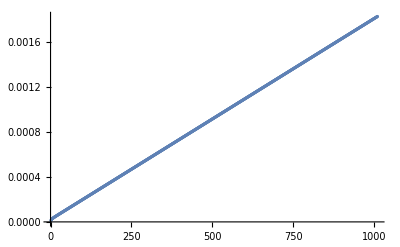

```mathematica
ListPlot[(a[[3]]-1)*100]
```